# Exact calculation of the partition function of the two-dimensional Ising model on an n × m square lattice.

This Mathematica code calculates the exact partition function of the two-dimensional Ising model on an n × m square lattice with periodic boundary conditions. Copyright: Paul D. Beale,  2010. 

The code is based on:
 	Paul D. Beale, Phys. Rev. Lett. 76, 78 (1996),
  		and Section 13.4.A of 
 	R.K. Pathria and Paul D. Beale, Statistical Mechanics, Third Edition (Academic, Boston, 2011).

The user's input parameters are two positive integers n and m specifying the numbers of rows and columns of the square lattice. The code has been tested on lattice sizes up to 128 × 128.
 
 The code calculates:
     
    	 z = Sum[g[[q + 1]] x^(2 q), {q, 0, n m}] = partition function defined in 
    	 	Pathria and Beale, equations 13.4.56, and 13.4.57 or 13.4.58
     
 	g[[q + 1]] = partition function coefficient which gives the number of microconfigurations with 
 		energy 4qJ above the ground state.
 		
 	x = Exp[-2K] is the Boltzmann factor for a single spin flip where K=J/kT
    
 	s[[q + 1]]=Log[g[[q+1]]] = microcanonical entropy for energy 4qJ above the ground state. 
 		The value of s=-∞ for some values of q since there are no states with that energy.
     
 
This code may be used for noncommercial purposes by referencing:
 	Paul D. Beale, Phys. Rev. Lett. 76, 78 (1996),
  		and
 	R.K. Pathria and Paul D. Beale, Statistical Mechanics, Third Edition (Academic, Boston, 2011).

The software is provided AS IS without warranty of any kind. 

Input n and m and evaluate the cell: 
	n is the number of rows and m is the number of columns. 
	The case n=1 (or m=1) gives the one-dimensional Ising model.

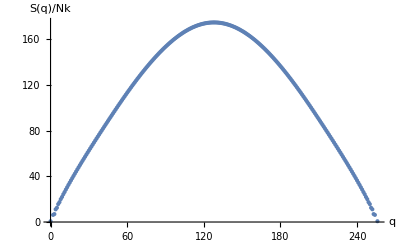

General::munfl: Exp[-794.455] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1193.76] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1589.57] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

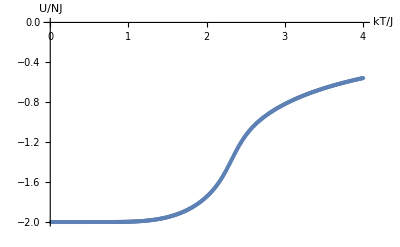

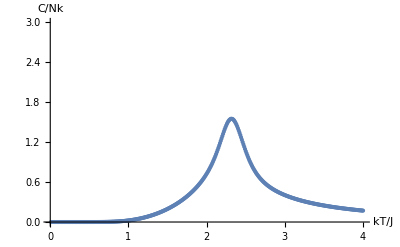

```mathematica
n = 16; m = 16;

ClearAll[acc,one,two,c0,cn,s0,sn,b,a,sum,bm,csqr,ssqr,z1,z2,z3,z4,z,g,kq,s,arg, p,ntemp, maxtemp,u,c,plotu,plotc];
(* Clear variables in case they are being used by the user. *)
acc = Floor[n m Log[2]/Log[10] + 50];  (* Set numerical accuracy more than sufficient to handle floating point numbers as large as the largest coefficients which are on the order 2^(n m) *)
one = SetPrecision[1, acc];
two = SetPrecision[2, acc];
(* See equation 13.4.59 for factors in partition function. *)
c0 = Expand[N[(one - one x)^m + (x (one + one x))^m, acc]]; s0 = Expand[N[(one - one x)^m - (x (one + one x))^m, acc]]; cn = Expand[N[(one + one x)^m + (x (one - one x))^m, acc]]; sn = Expand[N[(one + one x)^m - (x (one - one x))^m, acc]];
b = Expand[N[two  x (one - one x^2), acc]];
a = Table[Expand[N[(one + one x^2)^2 - b Cos[Pi q/n], acc]], {q, 1, n - 1}];
sum = Table[Expand[
    Sum[
     N[m!/(2 j)!/(m - 2 j)! (a[[q]]^2 - b^2)^j a[[q]]^(m - 2 j), acc]
     , {j, 0, Floor[m/2]}]]
   , {q, 1, n - 1}];
bm = Expand[b^m];
csqr = (sum + bm)/two^(m - 1);
ssqr = (sum - bm)/two^(m - 1);
(* Different formulae for partition function depending if the number of rows is even or odd. *)
If[Mod[n, 2] == 0,
(* even number of rows *)
 z1 = Expand[Product[csqr[[2 q + 1]], {q, 0, n/2 - 1}]/two];
 z2 = Expand[Product[ssqr[[2 q + 1]], {q, 0, n/2 - 1}]/two];
 z3 = Expand[c0 cn Product[csqr[[2 q]], {q, 1, n/2 - 1}]/two];
 z4 = Expand[s0 sn Product[ssqr[[2 q]], {q, 1, n/2 - 1}]/two];
 ,
(* odd number of rows *)
 z1 = Expand[cn Product[csqr[[2 q + 1]], {q, 0, (n - 3)/2}]/two];
 z2 = Expand[sn Product[ssqr[[2 q + 1]], {q, 0, (n - 3)/2}]/two];
 z3 = Expand[c0 Product[csqr[[2 q]], {q, 1, (n - 1)/2}]/two];
 z4 = Expand[s0 Product[ssqr[[2 q]], {q, 1, (n - 1)/2}]/two];
 ]
(* Calculate partition function, *)(* remove zero coeffiecients and make the rest integers. *)
z = Rationalize[Chop[z1 + z2 + z3 + z4, 10^(-20)]];
(* check solution *)
If[z /. x->1 ≠ 2^(n m ),Print["Error in Calculation: sum of g[[q]] not equal to 2^( n m) "]];
(* Put coefficients into a Table. *)
g = Table[2, {n m + 1}];
Do[g[[q + 1]] = Coefficient[z, x^(2 q)], {q, 1, n m}];
(* Determine the microcanonical entropy. *)
s = N[Log[g], 20];
(* Plot the microcanonical entropy. *)
kq=Table[q,{q,0, n m}];
splot=Table[{kq[[j]],s[[j]]},{j,1,n m + 1}];
ListPlot[splot,AxesLabel->{"q","S(q)/Nk"}]
(* Calculate and plot the internal energy per spin and the specific heat as functions of temperature. *)
maxtemp=4;
ntemp=(100)(maxtemp);
temp=Table[0.01 j,{j,1,ntemp}];
u=Table[0.0,{j,1,ntemp}];
c=Table[0.0,{j,1,ntemp}];

Do[arg=s-4 kq/temp[[j]];
(* Find the most probable energy for each temperature to maintain numerical precision. *)
maxarg=Max[arg];
p=Exp[arg-maxarg]/Apply[Plus,Exp[arg-maxarg]];u[[j]]=4Apply[Plus, kq p]/( n m) - 2;
c[[j]]=16/temp[[j]]^2(Apply[Plus, kq^2 p]-Apply[Plus, kq p]^2)/(n m),{j,1,ntemp}];
plotu=Table[{temp[[j]],u[[j]]},{j,1,ntemp}];
ListPlot[plotu,PlotRange->{{0,maxtemp},{-2,0}},AxesLabel->{kT/J,U/NJ}]
plotc=Table[{temp[[j]],c[[j]]},{j,1,ntemp}];
ListPlot[plotc,PlotRange->{{0,maxtemp},{0,3}},AxesLabel->{kT/J,C/Nk}]
(* Print the microcanonical entropy. *)
(* Some terms are -Infinity since g[[q]]= 0 for some values of q. *)
(* Print["s=",s] *)
(* Suppress printing the partition function and coefficients for large (n m) due to the size of the output. *)
(* If [ n m ≤ 256,Print["z=",z]] *)
(* If [ n m ≤ 256,Print["g=",g]] *)
```

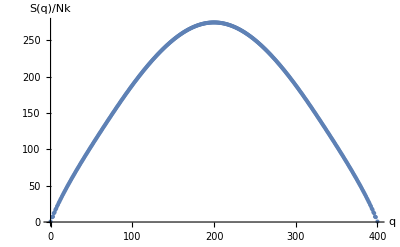

-Graphics-

```mathematica
LogDensity = Log[g];
LogDensity = DeleteCases[LogDensity, -Infinity];
MaxLw = Max[LogDensity];
LogConst = Log[Total[Exp[LogDensity - MaxLw]]] + MaxLw;
LogDensity = LogDensity - LogConst;
EnergyRange = Table[-2*n^2 + i, {i, 0, 4*n^2, 4}];
EnergyRange = DeleteCases[EnergyRange, -2*n^2 + 4];
EnergyRange = DeleteCases[EnergyRange, 2*n^2 - 4];
LogW = LogDensity - EnergyRange/2.3;
MaxLogW = Max[LogW];
FreeEnergy = -2.3 * (Log[Total[Exp[LogW - MaxLogW]]] + MaxLogW);
FreeEnergy/(n^2)
```

Table::iterb: Iterator {i,0,4 n^2,4} does not have appropriate bounds.

-(2.3 (0.-0.434783 Table[-2 n^2+i,{i,0,4 n^2,4}]))/n^2

```mathematica
Export["Logdensity.txt",N[Log[g], 10],"Table","FieldSeparators"->" "]
```

Logdensity.txt